```mathematica
SetDirectory[NotebookDirectory[]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"utility_generator_functions.nb"}]]
```

D:\Serious\FMI\Магистър\Дипломен семестър\Дипломна работа

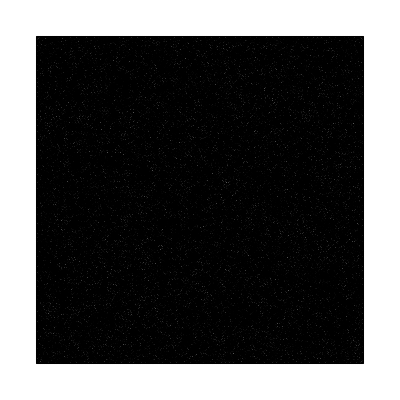

```mathematica
configPath="D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\";
SetDirectory[NotebookDirectory[]];
Get["utility_generator_functions.nb"];
Mcm=0.01;
(*TO DO: Fix the borders and source and MCM*)
left=-8;
right=8;
lower=-8;
middle=-11;
upper=8;
region=Rectangle[{left,lower},{right,upper}];
Needs["NDSolve`FEM`"];
em=ToElementMesh[region,"MeshOrder"->1,"MeshElementType"->"TriangleElement","MeshQualityGoal"->0.9,MaxCellMeasure->Mcm];
Show[em["Wireframe"]]
elements=em["MeshElements"][[1,1]];
nodes = em["Coordinates"];
elementsLen=Length[elements];
```

```mathematica
Length[nodes]
```

20518

```mathematica
a=1;
Plot3D[-2x*E^((-x^2-y^2)/a^2)/a^2,{x,-0.06,0.06},{y,-0.06,0.06},PlotRange->All]
```

-Graphics3D-

```mathematica
getLongestEdgeInMesh[nodes,elements]
minLen
```

0.21214

0.0878479

```mathematica
a=0.1;
Plot3D[-2x*E^((-x^2-y^2)/a^2)/a^2,{x,-2*minLen,2*minLen},{y,-2*minLen,2*minLen},PlotRange->All]
```

-Graphics3D-

```mathematica
findElementNearPoint[nodes,elements,0,0,0.1]
```

findElementNearPoint[{{-8.,-8.},{-8.,-7.9},{-8.,-7.8},{-8.,-7.7},{-8.,-7.6},{-8.,-7.5},{-8.,-7.4},{-8.,-7.3},{-8.,-7.2},{-8.,-7.1},{-8.,-7.},{-8.,-6.9},{-8.,-6.8},{-8.,-6.7},20490,{0.977373,2.02599},{-6.0367,-0.149308},{4.83205,4.75888},{4.17123,-3.17359},{4.17603,-3.26841},{4.34045,-3.27065},{-0.68124,-0.169725},{-0.636047,-0.263961},{6.28896,-5.35225},{-3.66678,0.798247},{-4.46846,0.508112},{-4.46783,1.01805},{0.483219,5.8898},{-5.99762,-5.55542}},3,0.1]
 |  |  |  |

```mathematica
coords=nodes[[elements[[%]]]]
```

{{-0.058298,-0.0419782},{0.0524192,-0.054345},{0.000145197,0.0528671}}

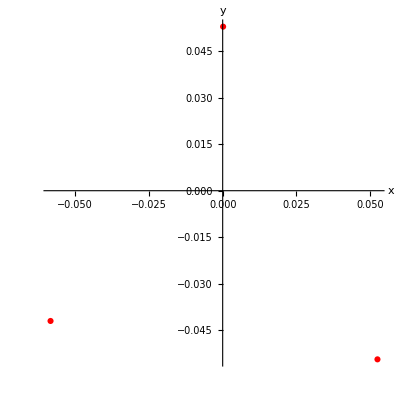

```mathematica
ListPlot[coords,PlotStyle->Red,PlotRange->All,AspectRatio->1,AxesLabel->{"x","y"},PlotMarkers->Automatic]
```

```mathematica
(*Check if mesh is ok*)
t = Table[{nodes[[i]],1},{i,1,Length[nodes]}];
(*Print["table: ",table];*)
intF = Interpolation[t,InterpolationOrder->1];
```

```mathematica
Length[elements]
Length[nodes]
getLongestEdgeInMesh[nodes,elements]
minLen
```

40394

20518

getLongestEdgeInMesh[{{-8.,-8.},{-8.,-7.9},{-8.,-7.8},{-8.,-7.7},{-8.,-7.6},{-8.,-7.5},{-8.,-7.4},{-8.,-7.3},{-8.,-7.2},{-8.,-7.1},{-8.,-7.},{-8.,-6.9},{-8.,-6.8},{-8.,-6.7},20490,{0.977373,2.02599},{-6.0367,-0.149308},{4.83205,4.75888},{4.17123,-3.17359},{4.17603,-3.26841},{4.34045,-3.27065},{-0.68124,-0.169725},{-0.636047,-0.263961},{6.28896,-5.35225},{-3.66678,0.798247},{-4.46846,0.508112},{-4.46783,1.01805},{0.483219,5.8898},{-5.99762,-5.55542}},{1}]
 |  |  |  |

minLen

```mathematica
setUpMeshForCpp[nodes,elements]
```

Exported nodes and elements

Found source

Resolved seismograh points

RegionMember::regp: A correctly specified region expected at position 1 of RegionMember[cavity,{-7.7,-7.92537}].

RegionMember::regp: A correctly specified region expected at position 1 of RegionMember[cavity,{-7.96667,-7.96667}].

RegionMember::regp: A correctly specified region expected at position 1 of RegionMember[cavity,{-7.,-7.90345}].

General::stop: Further output of RegionMember::regp will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

StringContainsQ::strse: String or list of strings expected at position 1 in StringContainsQ[List,=].

sourceElement

seismographIndices

mcm

tau

depths

left

right

cavityIndices

```mathematica
(*ANALYTICAL SOLUTION- NON CLOSED FORMULA*)
```

```mathematica
Transpose[100*{0.009070330660730633, 0.020150594959427115,0.05599184239491665,0.21937797617768676,0.36808136032746386}]
```

Transpose::nmtx: The first two levels of {0.907033,2.01506,5.59918,21.9378,36.8081} cannot be transposed.

Transpose[{0.907033,2.01506,5.59918,21.9378,36.8081}]

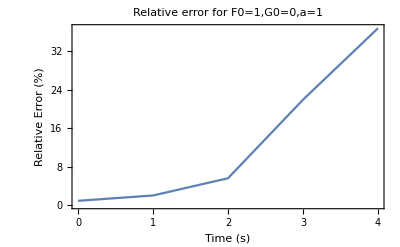

```mathematica
(*F0=1,G0=0,a=1*)
ListLinePlot[Transpose[{{0,1,2,3,4},100*{0.009070330660730633, 0.020150594959427115,0.05599184239491665,0.21937797617768676,0.36808136032746386}}],Frame->True,(*mcm decr*)
PlotLabel->"Relative error for F0=1,G0=0,a=1",
FrameLabel->{"Time (s)","Relative Error (%)"}]
```

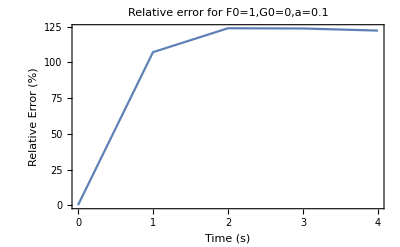

```mathematica
(*F0=1,G0=0,a=0.1*)
ListLinePlot[{{0,0.008816399198510839},{1,107.2365114925118},{2,124.00770325904645},{3,123.83342918136229},{4,122.3537533727853}},Frame->True,(*mcm decr*)
PlotLabel->"Relative error for F0=1,G0=0,a=0.1",
FrameLabel->{"Time (s)","Relative Error (%)"}]
```

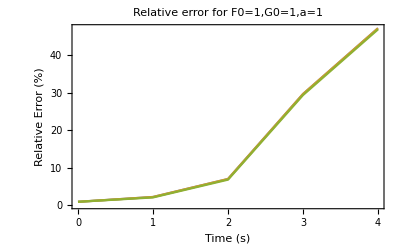

```mathematica
(*F0=1,G0=1,a=1*)
ListLinePlot[{{{0,0.8993288871136946},{1,2.1841131750711642},{2,6.991331499465037},{3,29.662990013993595},{4,47.225251156526493}},(*time decr*){{0,0.8993288871136946}, {1,2.1796031005327732},{2,6.986288826816063},{3,29.66058353559575},{4,47.210897384432077}},(*normal*){{0,0.8990063657394068},{1,2.0653048403975683},{2,6.811733485859701},{3,29.386889584609677},{4,46.9268337203621}}},Frame->True,(*mcm decr*)
PlotLabel->"Relative error for F0=1,G0=1,a=1",
FrameLabel->{"Time (s)","Relative Error (%)"}]
```

```mathematica
FourierTransform[-2x/((x^2+1)^2*(y^2+1)),{x,y},{w1,w2}]
```

-1/2 ⅈ ⅇ^(-w1-Abs[w2]) π w1 (ⅇ^(2 w1) HeavisideTheta[-w1]+HeavisideTheta[w1])

```mathematica
calculatePlot[q_,nodes_]:=Module[{n, table,T},(
T=Length[q];
ihat=Table[0,Length[q]];
n=Length[nodes];
For[j=1,j≤T,j++,
table = Table[{nodes[[i]],q[[j,i]]},{i,1,Length[nodes]}];
ihat[[j]] = Interpolation[table,InterpolationOrder->1];
];
ihat
)]
```

```mathematica
numericalSol=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\Eigen_seismogram_snapshots_0.01F1G1.csv","CSV"];
Dimensions[numericalSol]
table=Table[0,Length[numericalSol]];
n=Length[nodes];
For[j=1,j≤Length[numericalSol],j++,
table[[j]] = Table[(*nodes[[i]],*)numericalSol[[j,2*n+2*i-1]]^2+numericalSol[[j,2*n+2*i]]^2,{i,1,Length[nodes]}];
];
```

{5,82072}

```mathematica
calculatePlot[table,nodes];
numericalInterp=ihat;
```

```mathematica
matrixAnalyticalUx=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\uxx_all.csv","CSV"];
matrixAnalyticalUy=Import["D:\\Serious\\FMI\\Магистър\\Дипломен семестър\\FEM2D_config\\results\\uyy_all.csv","CSV"];
Dimensions[matrixAnalyticalUx ]

tableAnalytical=Table[0,Length[numericalSol]];

For[j=1,j≤Length[tableAnalytical],j++,
tableAnalytical[[j]] = Table[matrixAnalyticalUx[[j,i]]^2+matrixAnalyticalUy[[j,i]]^2,{i,1,Length[nodes]}];
];
```

{5,20518}

```mathematica
calculatePlot[tableAnalytical,nodes];
aalyticalInterp=ihat;
```

```mathematica
smallRegion=Rectangle[{-3,-3},{3,3}];
Manipulate[Plot3D[numericalInterp[[j]][x,y],{x,y}∈smallRegion,PlotRange->All],{j,1,Length[ihat],1}]

Manipulate[Plot3D[aalyticalInterp[[j]][x,y],{x,y}∈smallRegion,PlotRange->All],{j,1,Length[ihat],1}]
```

Part::partd: Part specification aalyticalInterp⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
Manipulate[Plot3D[2*Abs[x]*E^(-(x^2+y^2))^2-numericalInterp[[j]][x,y],{x,y}∈smallRegion,PlotRange->All],{j,1,Length[ihat],1}]
```

Plot3D::idomdim: {x,y}∈smallRegion does not have a valid dimension as a plotting domain.

Interpolation::innd: First argument in {} does not contain a list of data and coordinates.

General::stop: Further output of Interpolation::innd will be suppressed during this calculation.

Plot3D::idomdim: {x,y}∈smallRegion does not have a valid dimension as a plotting domain.

Part::partd: Part specification numericalInterp⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification numericalInterp⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
smallRegion=Rectangle[{-3,-3},{3,3}];
Plot3D[2*Sqrt[x^2+y^2]*E^(-(x^2+y^2)),{x,y}∈smallRegion,PlotRange->All]
```

-Graphics3D-

```mathematica
Plot3D[2*Sqrt[x^2/(1+x^2)^2+y^2/(1+y^2)^2]/((1+x^2)*(1+y^2)),{x,y}∈smallRegion,PlotRange->All]
```

-Graphics3D-

```mathematica
{xMin,xMax}={-3,3};
{yMin,yMax}={-3,3};
times=5;

(*Common plot style for analytic/numerical*)
plotStyle[fun_]:=Plot3D[fun[x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,ColorFunction->"NeonColors",Mesh->None,ImageSize->300,PlotPoints->50,ColorFunctionScaling->True,AxesLabel->{"x","y",""},PlotLegends->Automatic];
```

```mathematica
(*First row:analytic*)
rowAnalytic=Table[plotStyle[aalyticalInterp[[i]]],{i,Length[aalyticalInterp]}];

(*Second row:numerical*)
rowNumerical=Table[plotStyle[numericalInterp[[i]]],{i,Length[numericalInterp]}];
```

```mathematica
(*Third row:difference,with its own color scaling*)
rowDifference=Table[Plot3D[aalyticalInterp[[i]][x,y]-numericalInterp[[i]][x,y],{x,xMin,xMax},{y,yMin,yMax},PlotRange->All,(*match×10^-3 scale*)ColorFunction->"ThermometerColors",Mesh->None,ImageSize->285,PlotPoints->50,ColorFunctionScaling->True,AxesLabel->{"x","y",""},PlotLegends->Automatic],{i,Length[aalyticalInterp]}];
```

```mathematica
(*Put into a grid*)
GraphicsGrid[{rowAnalytic,rowNumerical,rowDifference},Spacings->{60,1},ImageSize->{2100,2100},Alignment->{Center,Center}]
```

-Graphics-